```mathematica
sensitivity and small angle approximation of the Log map for spheres
f[dot_]=ArcCos[dot]/Sqrt[1-dot^2]
```

and angle approximation for Log map of sensitivity small spheres the

ArcCos[dot]/(√(1-dot^2))

```mathematica
g[dot_]=ArcCos[dot]/Sin[ArcCos[dot]]
```

ArcCos[dot]/(√(1-dot^2))

```mathematica
Limit[f[dot],dot->-1]
```

∞

```mathematica
Limit[f[dot],dot->1]
```

1

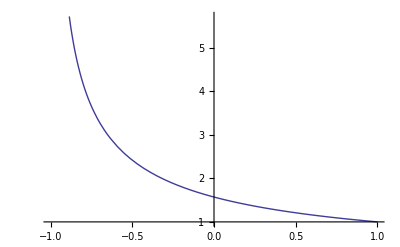

```mathematica
Plot[f[dot],{dot,-1,1}]
```

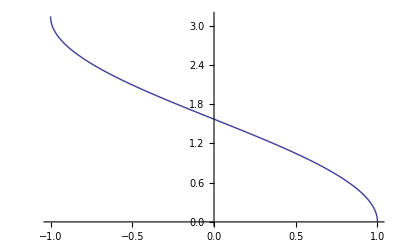

```mathematica
Plot[ArcCos[dot],{dot,-1,1}]
```

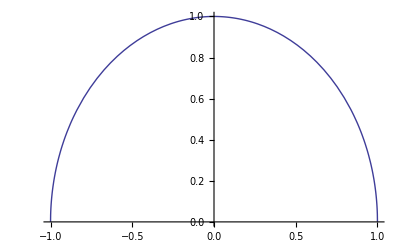

```mathematica
Plot[√(1-dot^2),{dot,-1,1}]
```

```mathematica
Series[f[dot],{dot,1,2}]
```

```mathematica
(-1)^Floor[-Arg[-1+dot]/(2 π)] (1-(dot-1)/3+2/15 (dot-1)^2+O[dot-1]^3)
```

```mathematica
Series[f[dot],{dot,1,1}]
```

(-1)^Floor[-Arg[-1+dot]/(2 π)] (1-(dot-1)/3+O[dot-1]^2)

```mathematica
Series[f[dot],{dot,-1,2}]
```

π/(√2 √(dot+1))-1+(π √(dot+1))/(4 √2)-(dot+1)/3+(3 π (dot+1)^(3/2))/(32 √2)-2/15 (dot+1)^2+O[dot+1]^(5/2)

```mathematica
Series[f[dot],{dot,-1,1}]
```

π/(√2 √(dot+1))-1+(π √(dot+1))/(4 √2)-(dot+1)/3+O[dot+1]^(3/2)

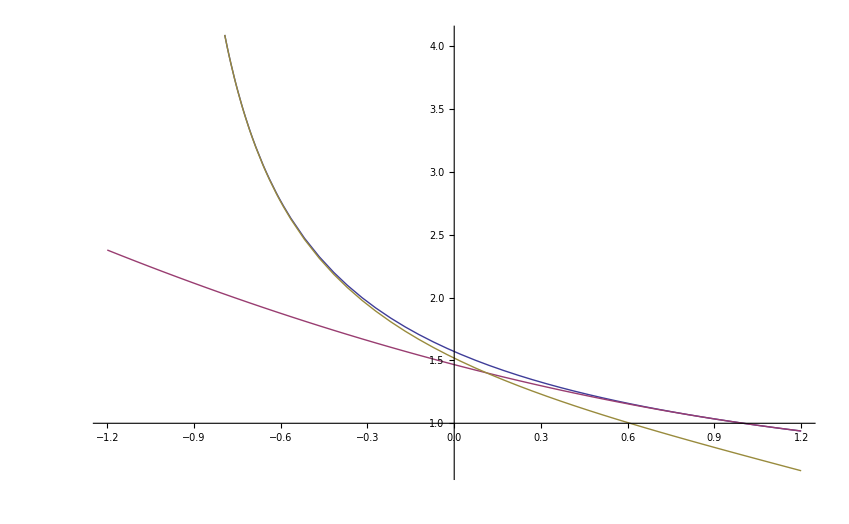

```mathematica
Plot[ {f[dot],(1-(dot-1)/3+2/15 (dot-1)^2),π/(√2 √(dot+1))-1+(π √(dot+1))/(4 √2)-(dot+1)/3+(3 π (dot+1)^(3/2))/(32 √2)-2/15 (dot+1)^2},{dot,-1.2,1.2}]
```

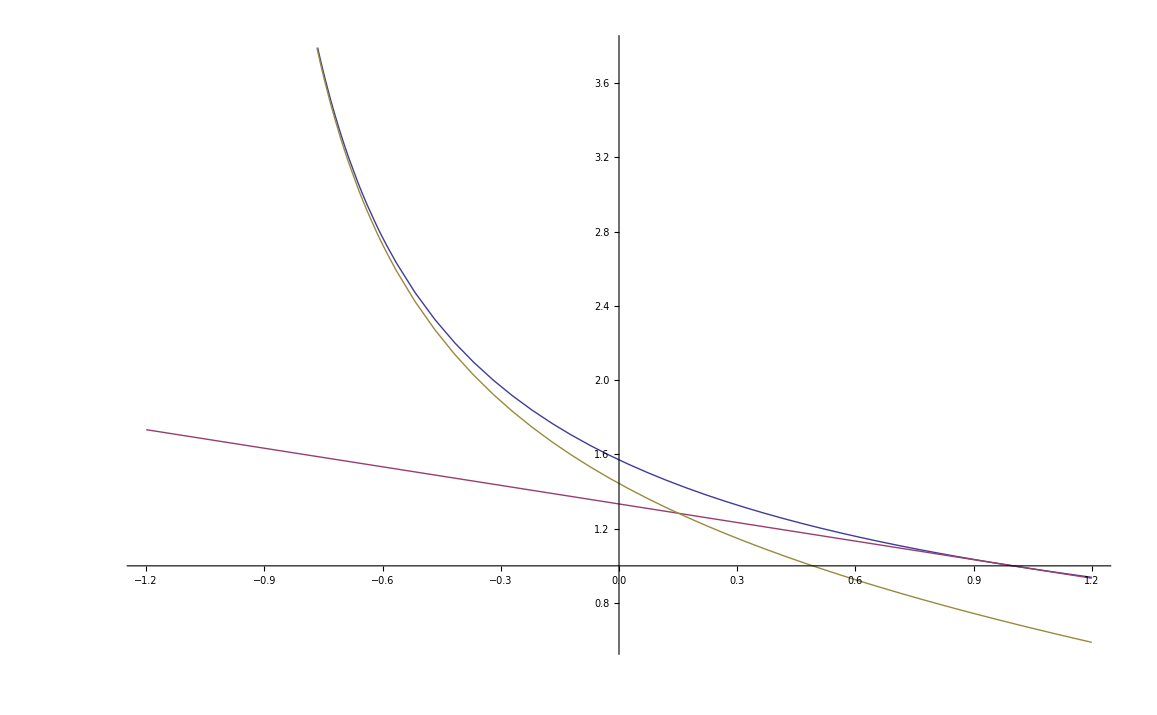

```mathematica
Plot[ {f[dot],(1-(dot-1)/3),π/(√2 √(dot+1))-1+(π √(dot+1))/(4 √2)-(dot+1)/3},{dot,-1.2,1.2}]
```